```mathematica
Needs["MaTeX`"];
(*PREDEFINED LABEL STYLE*)
labstyle={FontFamily->"Latin Modern Roman",FontSize->20};
magn=2;
IS=400;
thick=0.008;
thin=0.006;
dash={0.015,0.02};
pointsize=0.03;

(*decomposition code*)
(*Define Pauli matrices*)σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
id=IdentityMatrix[2];
(*Labels and matrices*)
pauliLabels={"I","σx","σy","σz"};
pauliMatrices={id,σx,σy,σz};

(*decomposition of 2 spins*)
n=2;
(*Generate all combinations*)
tuples=Tuples[Range[4],n];(*1-based indexing*)basisOps=KroneckerProduct@@@(pauliMatrices[[#]]&/@tuples);
basisLabels=StringRiffle[pauliLabels[[#]]&/@#," ⊗ "]&/@tuples;

(*Count number of non-identity terms*)
nonIdentityCounts=Count[#,x_/;x!=1]&/@tuples;
decompose1d[M_] := Tr[M. #]/2 & /@ {σx, σz}; (*a shorter single qubit decomp*)

(*Decomposition function*)
DecomposeSpinOperators[M_]:=Module[{coeffs,assoc,filtered},coeffs=Table[Tr[ConjugateTranspose[b].M]/8//FullSimplify,{b,basisOps}];
assoc=AssociationThread[Transpose[{basisLabels,nonIdentityCounts}]->coeffs];
filtered=Select[assoc,Chop[#]=!=0&];
<|"SingleQubitTerms"->KeySelect[filtered,#[[2]]==1&],"TwoQubitTerms"->KeySelect[filtered,#[[2]]==2&],"ThreeQubitTerms"->KeySelect[filtered,#[[2]]==3&]|>]
```

```mathematica
(*qubit parameters*)pars1={θ1->0.0,θ2->0.0,g1->53,g2->74,g3->47};

pars2={θ1->0.0,θ2->0.0,g1->60,g2->72,g3->43};
(*idle exchange for the aligned-axis case*)

Rot1=RotationMatrix[θ1,n1//Normalize];
Rot2=RotationMatrix[θ2,n2//Normalize];Jidle[gL_,gM_,gS_]:=((gM-gL)^2-(2 gS-gL-gM)^2)/(2 (2 gS-gL-gM))//N;
(*single-qubit Hamiltonian for qubit 1*)
Clear[H1,H2,Hint,Hfull];
H1[J12_,J23_]:=((1/2) (g1 KroneckerProduct[PauliMatrix[3],PauliMatrix[0],PauliMatrix[0]]+g2 KroneckerProduct[PauliMatrix[0],PauliMatrix[3],PauliMatrix[0]]+g3 KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[3]])+(1/4) Sum[J12 Rot1[[i,j]] KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+J23 Rot2[[i,j]] KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}])/. pars1;

(*single-qubit Hamiltonian for qubit 2*)
H2[J12_,J23_]:=((1/2) (g1 KroneckerProduct[PauliMatrix[3],PauliMatrix[0],PauliMatrix[0]]+g2 KroneckerProduct[PauliMatrix[0],PauliMatrix[3],PauliMatrix[0]]+g3 KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[3]])+(1/4) Sum[J12 Rot1[[i,j]] KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]]+J23 Rot2[[i,j]] KroneckerProduct[PauliMatrix[0],PauliMatrix[i],PauliMatrix[j]],{i,1,3},{j,1,3}])/. pars2;
Clear[Hint,Hfull];
parsint={
θint->0.00
}
n1={0,1,0};
n2={0,1,0};
nint={0,1,0};
Rotint=RotationMatrix[θint,nint//Normalize]/.parsint;
Hint[Jint_]:=(Jint/4 Sum[Rotint[[i,j]] KroneckerProduct[PauliMatrix[0],PauliMatrix[0],PauliMatrix[i],PauliMatrix[0],PauliMatrix[0],PauliMatrix[j]],{i,1,3},{j,1,3}])/. parsint;
Hfull[J12a_,J23a_,J12b_,J23b_,Jint_]:=KroneckerProduct[H1[J12a,J23a],IdentityMatrix[8]]+KroneckerProduct[IdentityMatrix[8],H2[J12b,J23b]]+Hint[Jint];


n1={0,1,0};
n2={0,1,0};

Rot1=RotationMatrix[θ1,Normalize[n1]];
Rot2=RotationMatrix[θ2,Normalize[n2]];

j12Guess1=Jidle[g1,g2,g3]/. pars1;
j12Guess2=Jidle[g1,g2,g3]/. pars2;

j23arr=Range[0,0.3,0.01];
j12arr1=Range[Max[0,j12Guess1-3.0],j12Guess1+3.0,0.01];
j12arr2=Range[Max[0,j12Guess2-3.0],j12Guess2+3.0,0.01];

X1=ParallelTable[With[{es=Eigensystem[N[H1[j12,j23]]]},Transpose[SortBy[Transpose[es],First]]],{j12,j12arr1},{j23,j23arr}];

eigval1=X1[[All,All,1]];
eigvect1=X1[[All,All,2]];
eigval1=eigval1-eigval1[[All,All,1]];

X2=ParallelTable[With[{es=Eigensystem[N[H2[j12,j23]]]},Transpose[SortBy[Transpose[es],First]]],{j12,j12arr2},{j23,j23arr}];

eigval2=X2[[All,All,1]];
eigvect2=X2[[All,All,2]];
eigval2=eigval2-eigval2[[All,All,1]];
```

{θint→0.}

$Aborted

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

$Aborted

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
ths=10^-3;

de1=eigval1[[All,All,3]]-eigval1[[All,All,2]];
pos1=Position[Chop[de1,ths],0];
curve1=Table[{j12arr1[[p[[1]]]],j23arr[[p[[2]]]]},{p,pos1}];

de2=eigval2[[All,All,3]]-eigval2[[All,All,2]];
pos2=Position[Chop[de2,ths],0];
curve2=Table[{j12arr2[[p[[1]]]],j23arr[[p[[2]]]]},{p,pos2}];

best1=First@MinimalBy[Flatten[Table[{j12arr1[[i]],j23arr[[j]],de1[[i,j]]},{i,Length[j12arr1]},{j,Length[j23arr]}],1],Last];

best2=First@MinimalBy[Flatten[Table[{j12arr2[[i]],j23arr[[j]],de2[[i,j]]},{i,Length[j12arr2]},{j,Length[j23arr]}],1],Last];

j12Idle1=best1[[1]];
j23Idle1=best1[[2]];
gapIdle1=best1[[3]];

j12Idle2=best2[[1]];
j23Idle2=best2[[2]];
gapIdle2=best2[[3]];

{j12Guess1,j12Idle1,j23Idle1,gapIdle1}
{j12Guess2,j12Idle2,j23Idle2,gapIdle2}
```

{9.81818,9.81818,0.,7.10543×10^-15}

{21.4348,21.4348,0.,7.10543×10^-15}

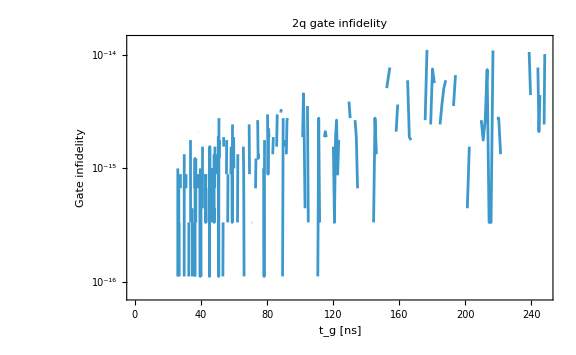

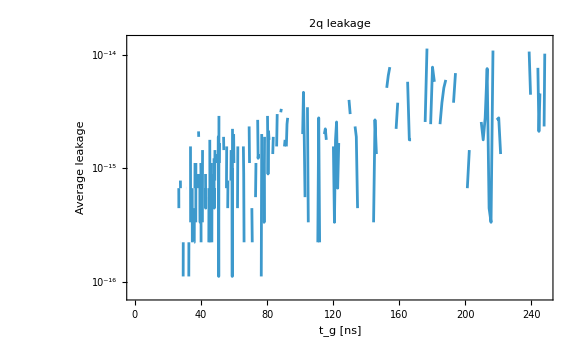

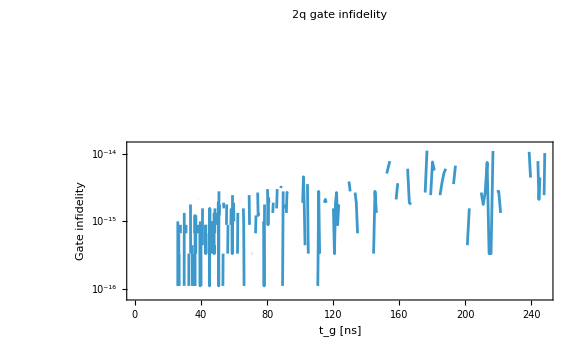

```mathematica
{i1,j1}=First@Position[de1,gapIdle1];
{i2,j2}=First@Position[de2,gapIdle2];

eigtot=KroneckerProduct[eigvect1[[i1,j1,2;;3]],eigvect2[[i2,j2,2;;3]]];

eigtotMatrix=N[Transpose[eigtot]];
Pcomp=eigtotMatrix.ConjugateTranspose[eigtotMatrix];

H1idle=N[H1[j12Idle1,j23Idle1]]//Chop;
H2idle=N[H2[j12Idle2,j23Idle2]]//Chop;

HidleFull=N[KroneckerProduct[H1idle,IdentityMatrix[8]]+KroneckerProduct[IdentityMatrix[8],H2idle]]//Chop;

HfullGate[Jint_]:=N[HidleFull+Hint[Jint]]//Chop;

Delta=(g3/. pars1)-(g3/. pars2);

tGate[Jint_]:=1/Sqrt[Delta^2+Jint^2];
tGateNs[Jint_]:=1000 tGate[Jint];

Utarget[Jint_]:=Module[{tg,a,c},tg=tGate[Jint];
a=2 Pi Jint tg/4;
c=2 Pi Delta tg/2;
DiagonalMatrix[{Exp[-I a],-Exp[I a+I c],-Exp[I a-I c],Exp[-I a]}]];


Uproj[Jint_]:=Module[{tg,U},tg=tGate[Jint];
U=MatrixExp[-I 2 Pi HfullGate[Jint] tg];
ConjugateTranspose[eigtotMatrix].U.eigtotMatrix];

gateFidelity[Jint_]:=Module[{K,Uid,d=4},K=Uproj[Jint];
Uid=Utarget[Jint];
Re[(Tr[ConjugateTranspose[K].K]+Abs[Tr[ConjugateTranspose[Uid].K]]^2)/(d (d+1))]];

gateInfidelity[Jint_]:=1-gateFidelity[Jint];

avgLeakage[Jint_]:=Module[{K,d=4},K=Uproj[Jint];
Re[1-Tr[ConjugateTranspose[K].K]/d]];

jintMin=0.5;
jintMax=40.0;
djint=0.05;

infidelityData=Table[{tGateNs[Jint],gateInfidelity[Jint]},{Jint,jintMin,jintMax,djint}];

leakageData=Table[{tGateNs[Jint],avgLeakage[Jint]},{Jint,jintMin,jintMax,djint}];

ListLogPlot[infidelityData,Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Gate infidelity"},PlotLabel->"2q gate infidelity",ImageSize->Large]

ListLogPlot[leakageData,Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Average leakage"},PlotLabel->"2q leakage",ImageSize->Large]
phiCPhase[Jint_]:=2 Pi Jint tGate[Jint];
phiCPhaseModPi[Jint_]:=Mod[phiCPhase[Jint],Pi];

longGatePoint2={202,10^-3};
shortGatePoint2={246,10^-3};

ListLogPlot[infidelityData,Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Gate infidelity"},PlotLabel->"2q gate infidelity",ImageSize->Large,Epilog->{Red,PointSize[0.02],Point[longGatePoint2],Point[shortGatePoint2],Black,Inset[Style[Row[{"ϕ = ",NumberForm[phiCPhaseModPi[jintMin]/Pi,{4,2}],"π"}],14,Background->White],{208,10^-3}],Inset[Style[Row[{"ϕ = ",NumberForm[phiCPhaseModPi[jintMax]/Pi,{4,2}],"π"}],14,Background->White],{238,10^-3}]}]
```

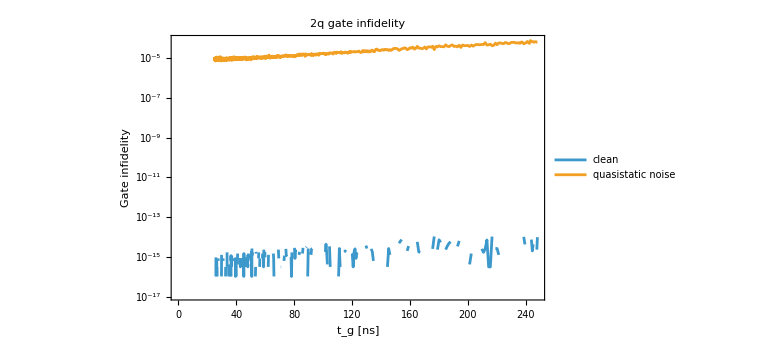

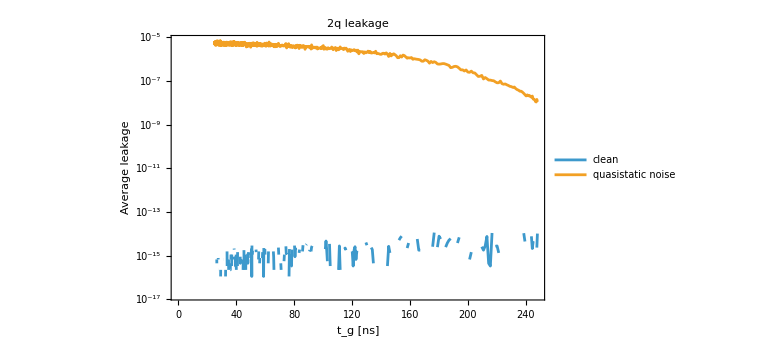

```mathematica
ClearAll[HdJ12Q1,HdJ12Q2,HdJ12Full1,HdJ12Full2,HintFull,UprojQS,oneSampleQS,averagedMetricsQS];

HdJ12Q1=N[(1/4) Sum[Rot1[[i,j]] KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]],{i,1,3},{j,1,3}]/. pars1]//Chop;

HdJ12Q2=N[(1/4) Sum[Rot1[[i,j]] KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[0]],{i,1,3},{j,1,3}]/. pars2]//Chop;

HdJ12Full1=KroneckerProduct[HdJ12Q1,IdentityMatrix[8]];
HdJ12Full2=KroneckerProduct[IdentityMatrix[8],HdJ12Q2];
HintFull=N[Hint[1.0]]//Chop;

sigmaJ12QS=5.3*10^-4;
sigmaJintQS=1.06*10^-3;

UprojQS[Jint_?NumericQ]:=Module[{tg,d1,d2,dint,Hnoisy,U},tg=tGate[Jint];
d1=RandomVariate[NormalDistribution[0,sigmaJ12QS]];
d2=RandomVariate[NormalDistribution[0,sigmaJ12QS]];
dint=RandomVariate[NormalDistribution[0,sigmaJintQS]];
Hnoisy=HidleFull+j12Idle1 d1 HdJ12Full1+j12Idle2 d2 HdJ12Full2+Jint (1+dint) HintFull;
U=MatrixExp[-I 2 Pi Hnoisy tg];
ConjugateTranspose[eigtotMatrix].U.eigtotMatrix];

oneSampleQS[Jint_?NumericQ]:=Module[{K,Uid,d=4,fidelity,leakage},K=UprojQS[Jint];
Uid=Utarget[Jint];
fidelity=Re[(Tr[ConjugateTranspose[K].K]+Abs[Tr[ConjugateTranspose[Uid].K]]^2)/(d (d+1))];
leakage=Re[1-Tr[ConjugateTranspose[K].K]/d];
<|"Infidelity"->1-fidelity,"Leakage"->leakage|>];

averagedMetricsQS[Jint_?NumericQ,nSamples_:200]:=Module[{samples},samples=Table[oneSampleQS[Jint],{nSamples}];
<|"Infidelity"->Mean[samples[[All,"Infidelity"]]],"Leakage"->Mean[samples[[All,"Leakage"]]]|>];

nSampQS=200;
jintList=Range[jintMin,jintMax,djint];

infidelityCleanData=Table[{tGateNs[Jint],gateInfidelity[Jint]},{Jint,jintList}];

leakageCleanData=Table[{tGateNs[Jint],avgLeakage[Jint]},{Jint,jintList}];

qsMetricsData=Table[With[{m=averagedMetricsQS[Jint,nSampQS]},{tGateNs[Jint],m["Infidelity"],m["Leakage"]}],{Jint,jintList}];

infidelityQSData=qsMetricsData[[All,{1,2}]];
leakageQSData=qsMetricsData[[All,{1,3}]];

ListLogPlot[{infidelityCleanData,infidelityQSData},Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Gate infidelity"},PlotLabel->"2q gate infidelity",PlotLegends->{"clean","quasistatic noise"},ImageSize->Large]

ListLogPlot[{leakageCleanData,leakageQSData},Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Average leakage"},PlotLabel->"2q leakage",PlotLegends->{"clean","quasistatic noise"},ImageSize->Large]
```

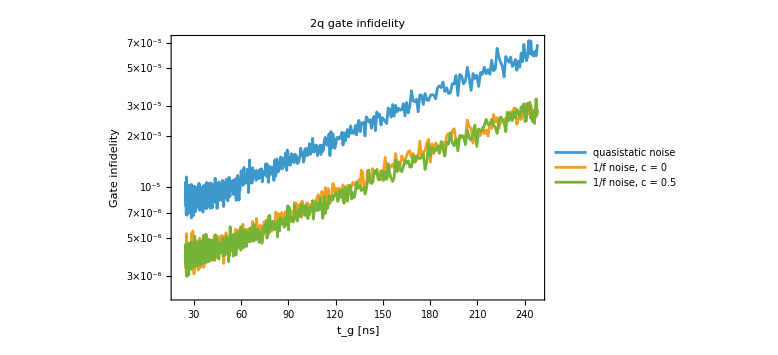

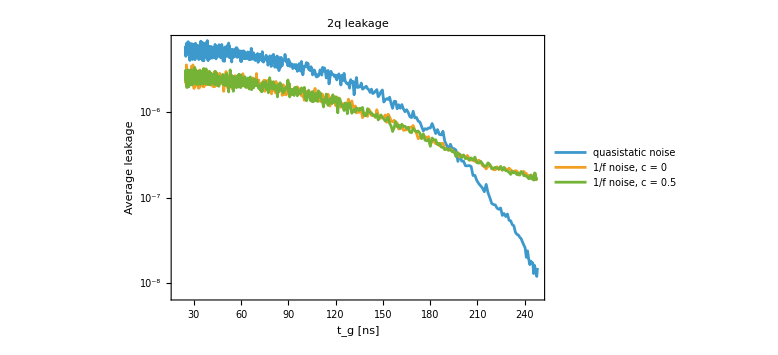

```mathematica
ClearAll[noiseTrace1f,oneSample1fCorr,averagedMetrics1fCorr];

ClearAll[noiseTrace1fAlpha,gateDts,oneSample1fCorr,averagedMetrics1fCorr];

noiseTrace1fAlpha[amp1Hz_,tExpUs_:1.,dtStepUs_:0.0005,fLowHz_:1.,alpha_:1.,window_:100]:=Module[{nPts,fNyqHz,edgesHz,fMHz,binPower,phi,a},nPts=Ceiling[tExpUs/dtStepUs];
fNyqHz=10.^6/(2 dtStepUs);
edgesHz=Exp@Subdivide[Log[fLowHz],Log[fNyqHz],window];
fMHz=Sqrt[Most[edgesHz] Rest[edgesHz]]/10.^6;
binPower=If[PossibleZeroQ[alpha-1],Log[Rest[edgesHz]/Most[edgesHz]],(Rest[edgesHz]^(1-alpha)-Most[edgesHz]^(1-alpha))/(1-alpha)];
phi=RandomReal[{0,2 Pi},window];
a=amp1Hz Sqrt[binPower];
Table[Total[a Cos[2 Pi fMHz (k dtStepUs)+phi]],{k,0,nPts-1}]];

gateDts[tg_,dtStepUs_]:=Module[{n=Max[1,Ceiling[tg/dtStepUs]]},Join[ConstantArray[dtStepUs,n-1],{tg-(n-1) dtStepUs}]];

oneSample1fCorr[Jint_?NumericQ,ampJ12_:2.5*10^-4,ampJint_:5*10^-4,corr_:0.5,tExpUs_:1.,dtStepUs_:0.0005,alpha_:1.,window_:100]:=Module[{tg,dts,nSeg,nCommon,nLocal12a,nLocal12b,nLocalInt,n12a,n12b,nint,U,K,Uid,d=4,fid,leak},tg=tGate[Jint];
If[tg>tExpUs,Return[<|"Infidelity"->Indeterminate,"Leakage"->Indeterminate|>]];
dts=gateDts[tg,dtStepUs];
nSeg=Length[dts];
nCommon=Take[noiseTrace1fAlpha[1.,tExpUs,dtStepUs,1.,alpha,window],nSeg];
nLocal12a=Take[noiseTrace1fAlpha[1.,tExpUs,dtStepUs,1.,alpha,window],nSeg];
nLocal12b=Take[noiseTrace1fAlpha[1.,tExpUs,dtStepUs,1.,alpha,window],nSeg];
nLocalInt=Take[noiseTrace1fAlpha[1.,tExpUs,dtStepUs,1.,alpha,window],nSeg];
n12a=ampJ12 (Sqrt[corr] nCommon+Sqrt[1-corr] nLocal12a);
n12b=ampJ12 (Sqrt[corr] nCommon+Sqrt[1-corr] nLocal12b);
nint=ampJint (Sqrt[corr] nCommon+Sqrt[1-corr] nLocalInt);
U=Fold[Dot,IdentityMatrix[Length[HidleFull]],Reverse@MapThread[MatrixExp[-I 2 Pi #1 (HidleFull+j12Idle1 #2 HdJ12Full1+j12Idle2 #3 HdJ12Full2+Jint (1+#4) HintFull)]&,{dts,n12a,n12b,nint}]];
K=ConjugateTranspose[eigtotMatrix].U.eigtotMatrix;
Uid=Utarget[Jint];
fid=Re[(Tr[ConjugateTranspose[K].K]+Abs[Tr[ConjugateTranspose[Uid].K]]^2)/(d (d+1))];
leak=Re[1-Tr[ConjugateTranspose[K].K]/d];
<|"Infidelity"->1-fid,"Leakage"->leak|>];

averagedMetrics1fCorr[Jint_?NumericQ,ampJ12_:2.5*10^-4,ampJint_:5*10^-4,corr_:0.5,tExpUs_:1.,dtStepUs_:0.0005,nSamples_:20,alpha_:1.,window_:100]:=Module[{samples},samples=Table[oneSample1fCorr[Jint,ampJ12,ampJint,corr,tExpUs,dtStepUs,alpha,window],{nSamples}];
<|"Infidelity"->Mean[samples[[All,"Infidelity"]]],"Leakage"->Mean[samples[[All,"Leakage"]]]|>];

ampJ12=2.5*10^-4;
ampJ23=1.3*10^-3;
ampJint=5*10^-4;

tExpUs=1.;
dtStepUs=0.0005;   (*0.5 ns*)
nSamples=200;
alphaNoise=1.;
window=100;

infidelityQSData=Table[{tGateNs[Jint],averagedMetricsQS[Jint,nSampQS]["Infidelity"]},{Jint,jintMin,jintMax,djint}];

leakageQSData=Table[{tGateNs[Jint],averagedMetricsQS[Jint,nSampQS]["Leakage"]},{Jint,jintMin,jintMax,djint}];

metrics1fUncorrData=Table[With[{m=averagedMetrics1fCorr[Jint,ampJ12,ampJint,0.,tExpUs,dtStepUs,nSamples,alphaNoise,window]},{tGateNs[Jint],m["Infidelity"],m["Leakage"]}],{Jint,jintMin,jintMax,djint}];

metrics1fHalfCorrData=Table[With[{m=averagedMetrics1fCorr[Jint,ampJ12,ampJint,0.5,tExpUs,dtStepUs,nSamples,alphaNoise,window]},{tGateNs[Jint],m["Infidelity"],m["Leakage"]}],{Jint,jintMin,jintMax,djint}];

infidelity1fUncorrData=metrics1fUncorrData[[All,{1,2}]];
leakage1fUncorrData=metrics1fUncorrData[[All,{1,3}]];

infidelity1fHalfCorrData=metrics1fHalfCorrData[[All,{1,2}]];
leakage1fHalfCorrData=metrics1fHalfCorrData[[All,{1,3}]];

ListLogPlot[{infidelityQSData,infidelity1fUncorrData,infidelity1fHalfCorrData},Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Gate infidelity"},PlotLabel->"2q gate infidelity",PlotLegends->{"quasistatic noise","1/f noise, c = 0","1/f noise, c = 0.5"},ImageSize->Large,PlotRange->All]

ListLogPlot[{leakageQSData,leakage1fUncorrData,leakage1fHalfCorrData},Frame->True,Joined->True,FrameLabel->{"t_g [ns]","Average leakage"},PlotLabel->"2q leakage",PlotLegends->{"quasistatic noise","1/f noise, c = 0","1/f noise, c = 0.5"},ImageSize->Large,PlotRange->All]
```

```mathematica
(*Export["/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_clean.csv",infidelityCleanData];
Export["/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_qs.csv",infidelityQSData];
RunProcess[{"/opt/anaconda3/bin/python3","/Users/tivakhtel/SOSO-qubit/tess_code/plot_2q_infidelity_prx.py","--clean","/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_clean.csv","--noisy","/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_qs.csv","--output","/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_qs_vs_clean_prx.pdf","--clean-label","Clean","--noisy-label","Quasistatic noise"}]*)
```

<|ExitCode→0,StandardOutput→,StandardError→|>

```mathematica
Export["/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_qs.csv",infidelityQSData];
Export["/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_1f_uncorr.csv",infidelity1fUncorrData];
Export["/Users/tivakhtel/SOSO-qubit/tess_code/infidelity_1f_halfcorr.csv",infidelity1fHalfCorrData];
Export["/Users/tivakhtel/SOSO-qubit/tess_code/leakage_qs.csv",leakageQSData];
Export["/Users/tivakhtel/SOSO-qubit/tess_code/leakage_1f_uncorr.csv",leakage1fUncorrData];
Export["/Users/tivakhtel/SOSO-qubit/tess_code/leakage_1f_halfcorr.csv",leakage1fHalfCorrData];
```